```mathematica
(* pie chart in Fig 1D *)
(* Sevahn Vorperian, Quake Lab *)
```

```mathematica
(* copying everything over here that is working because other notebook is a mess *)
```

```mathematica
fractions = Import["/Users/kayaneh/Documents/peeproject/code/deconvolve_urine/average_normal_sediment_fractions_noN4_20230518.csv"];
```

```mathematica
roundPower = 0.1;
percentThresh = 1.1; (* percentage cutoff for stacked bar chart vs main pie *)
scalePercents = 100; (* scale all percentages by 100 *)
superSmallThresh = 0.3; (* percentage cutoff for cell types with small fractional contirbutions *)
sampleCenter = "Normal Sediment Average";
```

```mathematica
fractions
```

{{,0},{Kidney epithelial cell,0.122644},{Keratinocyte,0.0975791},{Prostate epithelia,0.0771632},{Salivary gland cell,0.0677399},{Intestinal enterocyte,0.0497572},{Mature conventional dendritic cell,0.0479099},{Ionocyte/luminal epithelial cell of mammary gland,0.045542},{Luminal cell of prostate epithelium,0.0398409},{Intestinal tuft cell,0.0385681},{Neutrophil,0.0369175},{B cell,0.0316764},{Intrahepatic cholangiocyte,0.0312018},{Macrophage,0.0287973},{Bladder urothelial cell,0.0267929},{Monocyte,0.0261963},{Plasmablast,0.0216179},{Stromal cell,0.0185583},{Respiratory ciliated cell,0.016987},{Schwann cell,0.0159544},{Basal cell,0.0154336},{Pericyte cell,0.0129426},{Salivary/bronchial secretory cell,0.0110896},{Hepatocyte,0.0109849},{Endothelial cell,0.0101755},{Thymocyte,0.00915216},{Mesothelial cell,0.00856229},{Intestinal secretory cell,0.00835211},{Nk cell,0.00769062},{Myeloid progenitor,0.0076417},{Goblet cell,0.00730011},{T cell,0.0071069},{Pulmonary ionocyte,0.00671186},{Adventitial cell,0.00610018},{Tendon cell,0.00396568},{Mast cell,0.00372022},{Fibroblast/mesenchymal stem cell,0.00369649},{Pancreatic pp cell,0.00338415},{Club cell/type i pneumocyte,0.00266731},{Cell of skeletal muscle,0.00246193},{Basal cell of prostate epithelium,0.00209686},{Duodenum glandular cell,0.00178054},{Type ii pneumocyte,0.0014932},{Platelet,0.00137414},{Hematopoietic stem cell,0.000875075},{Smooth muscle cell,0.000563367},{Pancreatic delta cell,0.000447909},{Erythrocyte/erythroid progenitor,0.000345798},{Pancreatic ductal cell,0.000243139},{Secretory cell,0.000103418},{Pancreatic alpha/beta cell,0.0000622659},{Gland cell,0.000030573}}

```mathematica
fractions = fractions[[2;;]]; (* eliminate the center name *)
```

```mathematica
(* cellTypes = fractions[[1]][[2;;]] *)
cellTypes = fractions[[;;,1]]
```

{Kidney epithelial cell,Keratinocyte,Prostate epithelia,Salivary gland cell,Intestinal enterocyte,Mature conventional dendritic cell,Ionocyte/luminal epithelial cell of mammary gland,Luminal cell of prostate epithelium,Intestinal tuft cell,Neutrophil,B cell,Intrahepatic cholangiocyte,Macrophage,Bladder urothelial cell,Monocyte,Plasmablast,Stromal cell,Respiratory ciliated cell,Schwann cell,Basal cell,Pericyte cell,Salivary/bronchial secretory cell,Hepatocyte,Endothelial cell,Thymocyte,Mesothelial cell,Intestinal secretory cell,Nk cell,Myeloid progenitor,Goblet cell,T cell,Pulmonary ionocyte,Adventitial cell,Tendon cell,Mast cell,Fibroblast/mesenchymal stem cell,Pancreatic pp cell,Club cell/type i pneumocyte,Cell of skeletal muscle,Basal cell of prostate epithelium,Duodenum glandular cell,Type ii pneumocyte,Platelet,Hematopoietic stem cell,Smooth muscle cell,Pancreatic delta cell,Erythrocyte/erythroid progenitor,Pancreatic ductal cell,Secretory cell,Pancreatic alpha/beta cell,Gland cell}

```mathematica
(* fractions =fractions[[2;;,2;;]][[1]] *)
fractions = fractions[[;;,2]]
```

{0.122644,0.0975791,0.0771632,0.0677399,0.0497572,0.0479099,0.045542,0.0398409,0.0385681,0.0369175,0.0316764,0.0312018,0.0287973,0.0267929,0.0261963,0.0216179,0.0185583,0.016987,0.0159544,0.0154336,0.0129426,0.0110896,0.0109849,0.0101755,0.00915216,0.00856229,0.00835211,0.00769062,0.0076417,0.00730011,0.0071069,0.00671186,0.00610018,0.00396568,0.00372022,0.00369649,0.00338415,0.00266731,0.00246193,0.00209686,0.00178054,0.0014932,0.00137414,0.000875075,0.000563367,0.000447909,0.000345798,0.000243139,0.000103418,0.0000622659,0.000030573}

```mathematica
Length[fractions]
```

51

```mathematica
Length[cellTypes]
```

51

```mathematica
(* fractions = Import["~/Documents/deconvolution/cellTypeFractions_10XDecon_07222020.xlsx"][[1]]; *)
```

```mathematica
contribs = fractions  (* excluded sample name and r, p-value, RMSE *)
```

{0.122644,0.0975791,0.0771632,0.0677399,0.0497572,0.0479099,0.045542,0.0398409,0.0385681,0.0369175,0.0316764,0.0312018,0.0287973,0.0267929,0.0261963,0.0216179,0.0185583,0.016987,0.0159544,0.0154336,0.0129426,0.0110896,0.0109849,0.0101755,0.00915216,0.00856229,0.00835211,0.00769062,0.0076417,0.00730011,0.0071069,0.00671186,0.00610018,0.00396568,0.00372022,0.00369649,0.00338415,0.00266731,0.00246193,0.00209686,0.00178054,0.0014932,0.00137414,0.000875075,0.000563367,0.000447909,0.000345798,0.000243139,0.000103418,0.0000622659,0.000030573}

```mathematica
Length[fractions]
```

51

```mathematica
Length[cellTypes]
```

51

```mathematica
(* first get the zero index *)
```

```mathematica
zeroIndex = Position[contribs, val_/;val ≤ 0]
```

{}

```mathematica
(* drop it from the contributions and drop the corresponding labels *)
```

```mathematica
nonZeroVals = Delete[contribs, zeroIndex];
```

```mathematica
nonZeroVals = nonZeroVals * scalePercents
```

{12.2644,9.75791,7.71632,6.77399,4.97572,4.79099,4.5542,3.98409,3.85681,3.69175,3.16764,3.12018,2.87973,2.67929,2.61963,2.16179,1.85583,1.6987,1.59544,1.54336,1.29426,1.10896,1.09849,1.01755,0.915216,0.856229,0.835211,0.769062,0.76417,0.730011,0.71069,0.671186,0.610018,0.396568,0.372022,0.369649,0.338415,0.266731,0.246193,0.209686,0.178054,0.14932,0.137414,0.0875075,0.0563367,0.0447909,0.0345798,0.0243139,0.0103418,0.00622659,0.0030573}

```mathematica
Total[nonZeroVals]
```

100.

```mathematica
nonZeroCells = Delete[cellTypes, zeroIndex];
```

```mathematica
Length[nonZeroCells]
```

51

```mathematica
nonZeroCells
```

{Kidney epithelial cell,Keratinocyte,Prostate epithelia,Salivary gland cell,Intestinal enterocyte,Mature conventional dendritic cell,Ionocyte/luminal epithelial cell of mammary gland,Luminal cell of prostate epithelium,Intestinal tuft cell,Neutrophil,B cell,Intrahepatic cholangiocyte,Macrophage,Bladder urothelial cell,Monocyte,Plasmablast,Stromal cell,Respiratory ciliated cell,Schwann cell,Basal cell,Pericyte cell,Salivary/bronchial secretory cell,Hepatocyte,Endothelial cell,Thymocyte,Mesothelial cell,Intestinal secretory cell,Nk cell,Myeloid progenitor,Goblet cell,T cell,Pulmonary ionocyte,Adventitial cell,Tendon cell,Mast cell,Fibroblast/mesenchymal stem cell,Pancreatic pp cell,Club cell/type i pneumocyte,Cell of skeletal muscle,Basal cell of prostate epithelium,Duodenum glandular cell,Type ii pneumocyte,Platelet,Hematopoietic stem cell,Smooth muscle cell,Pancreatic delta cell,Erythrocyte/erythroid progenitor,Pancreatic ductal cell,Secretory cell,Pancreatic alpha/beta cell,Gland cell}

```mathematica
nonZeroVals
```

{12.2644,9.75791,7.71632,6.77399,4.97572,4.79099,4.5542,3.98409,3.85681,3.69175,3.16764,3.12018,2.87973,2.67929,2.61963,2.16179,1.85583,1.6987,1.59544,1.54336,1.29426,1.10896,1.09849,1.01755,0.915216,0.856229,0.835211,0.769062,0.76417,0.730011,0.71069,0.671186,0.610018,0.396568,0.372022,0.369649,0.338415,0.266731,0.246193,0.209686,0.178054,0.14932,0.137414,0.0875075,0.0563367,0.0447909,0.0345798,0.0243139,0.0103418,0.00622659,0.0030573}

```mathematica
(* nonZeroVals = nonZeroVals/Total[nonZeroVals] (* normalize to 1 *) did this normalization in python *)
```

```mathematica
nonZeroVals = Round[#, roundPower] &/@nonZeroVals (* round to 3 digits *)
```

{12.3,9.8,7.7,6.8,5.,4.8,4.6,4.,3.9,3.7,3.2,3.1,2.9,2.7,2.6,2.2,1.9,1.7,1.6,1.5,1.3,1.1,1.1,1.,0.9,0.9,0.8,0.8,0.8,0.7,0.7,0.7,0.6,0.4,0.4,0.4,0.3,0.3,0.2,0.2,0.2,0.1,0.1,0.1,0.1,0.,0.,0.,0.,0.,0.}

```mathematica
Total[nonZeroVals]
```

100.2

```mathematica
(* get index cell types that are less than one percent together for the bar chart *)
```

```mathematica
lt1Percent = Position[nonZeroVals, val_/;val  < percentThresh]
```

{{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51}}

```mathematica
(* now pull the cell types and their associated values and put in reverse order so it goes from smallest to largest *)
```

```mathematica
smallContribVals = Reverse[Part[nonZeroVals, # ]&/@ lt1Percent]
smallContribCells = Reverse[Part[nonZeroCells, #] &/@ lt1Percent];
```

{{0.},{0.},{0.},{0.},{0.},{0.},{0.1},{0.1},{0.1},{0.1},{0.2},{0.2},{0.2},{0.3},{0.3},{0.4},{0.4},{0.4},{0.6},{0.7},{0.7},{0.7},{0.8},{0.8},{0.8},{0.9},{0.9},{1.}}

```mathematica
(* get the indices where the elements are ≤ 0.1% or 0.001 *)
```

```mathematica
ltPt1Percent = Position[Flatten[smallContribVals], val_/;val  ≤ superSmallThresh]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15}}

```mathematica
(* get the sum of the values and the respective cell ≤ 0.1 % *)
fracsLTPt1 = Part[smallContribVals, # ] &/@ ltPt1Percent
cellsLTPt1 = Part[smallContribCells, #] &/@ ltPt1Percent
```

{{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.1}},{{0.1}},{{0.1}},{{0.1}},{{0.2}},{{0.2}},{{0.2}},{{0.3}},{{0.3}}}

{{{Gland cell}},{{Pancreatic alpha/beta cell}},{{Secretory cell}},{{Pancreatic ductal cell}},{{Erythrocyte/erythroid progenitor}},{{Pancreatic delta cell}},{{Smooth muscle cell}},{{Hematopoietic stem cell}},{{Platelet}},{{Type ii pneumocyte}},{{Duodenum glandular cell}},{{Basal cell of prostate epithelium}},{{Cell of skeletal muscle}},{{Club cell/type i pneumocyte}},{{Pancreatic pp cell}}}

```mathematica
totalSuperSmall = Total[Flatten[fracsLTPt1]]
```

1.6

```mathematica
(* now drop those small guys *)
```

```mathematica
goodSmallVals = Delete[smallContribVals, ltPt1Percent];
goodSmallCells = Delete[smallContribCells, ltPt1Percent];
```

```mathematica
goodSmallCells
```

{{Fibroblast/mesenchymal stem cell},{Mast cell},{Tendon cell},{Adventitial cell},{Pulmonary ionocyte},{T cell},{Goblet cell},{Myeloid progenitor},{Nk cell},{Intestinal secretory cell},{Mesothelial cell},{Thymocyte},{Endothelial cell}}

```mathematica
(* add the sum of the remaining cells *)
goodSmallVals = AppendTo[goodSmallVals, {totalSuperSmall}]
goodSmallCells = AppendTo[goodSmallCells, {"Very Small Contributors"}]
```

{{0.4},{0.4},{0.4},{0.6},{0.7},{0.7},{0.7},{0.8},{0.8},{0.8},{0.9},{0.9},{1.},{1.6}}

{{Fibroblast/mesenchymal stem cell},{Mast cell},{Tendon cell},{Adventitial cell},{Pulmonary ionocyte},{T cell},{Goblet cell},{Myeloid progenitor},{Nk cell},{Intestinal secretory cell},{Mesothelial cell},{Thymocyte},{Endothelial cell},{Very Small Contributors}}

```mathematica
(* now sort this finalized "small cell" list *)
```

```mathematica
finalOrder = Reverse[Ordering[goodSmallVals]]
```

{14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
goodSmallVals = Flatten[Part[goodSmallVals , #] &/@ finalOrder]
```

{1.6,1.,0.9,0.9,0.8,0.8,0.8,0.7,0.7,0.7,0.6,0.4,0.4,0.4}

```mathematica
goodSmallCells = Flatten[Part[goodSmallCells, #] &/@ finalOrder]
```

{Very Small Contributors,Endothelial cell,Thymocyte,Mesothelial cell,Intestinal secretory cell,Nk cell,Myeloid progenitor,Goblet cell,T cell,Pulmonary ionocyte,Adventitial cell,Tendon cell,Mast cell,Fibroblast/mesenchymal stem cell}

```mathematica
(* now make the bar chart *)
```

```mathematica
shortlist =List[Flatten[Table[Callout[goodSmallVals[[#]], goodSmallCells[[#]],After,Appearance->"Leader",LeaderSize->{15,Automatic,2}],1] &/@Range[Length[goodSmallCells]]]];
```

```mathematica
shortlist
```

{{Callout[1.6,Very Small Contributors,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[1.,Endothelial cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.9,Thymocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.9,Mesothelial cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.8,Intestinal secretory cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.8,Nk cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.8,Myeloid progenitor,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,Goblet cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,T cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,Pulmonary ionocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.6,Adventitial cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.4,Tendon cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.4,Mast cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.4,Fibroblast/mesenchymal stem cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}]}}

```mathematica
piePal = Map [RGBColor,{"#0D3b66","#bee9e8","#62b6cb","#1b4965","#cae9ff","#5fa8d3","#f25c54","#EE964B","#f25c54", "#f26419", "#a4508b", "#f7567c","#7e1946", "#f6ae2d", "#68b0ab", "#5bba6f", "#9ece9a", "#c8d5b9","#b56576","#FFBF81","#FFD9CE"}]
```

{RGBColor[0.050980392156862744, 0.23137254901960785, 0.4],RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.10588235294117647, 0.28627450980392155, 0.396078431372549],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.9490196078431372, 0.3607843137254902, 0.32941176470588235],RGBColor[0.9333333333333333, 0.5882352941176471, 0.29411764705882354],RGBColor[0.9490196078431372, 0.3607843137254902, 0.32941176470588235],RGBColor[0.9490196078431372, 0.39215686274509803, 0.09803921568627451],RGBColor[0.6431372549019608, 0.3137254901960784, 0.5450980392156862],RGBColor[0.9686274509803922, 0.33725490196078434, 0.48627450980392156],RGBColor[0.49411764705882355, 0.09803921568627451, 0.27450980392156865],RGBColor[0.9647058823529412, 0.6823529411764706, 0.17647058823529413],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.3568627450980392, 0.7294117647058823, 0.43529411764705883],RGBColor[0.6196078431372549, 0.807843137254902, 0.6039215686274509],RGBColor[0.7843137254901961, 0.8352941176470589, 0.7254901960784313],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[1., 0.7490196078431373, 0.5058823529411764],RGBColor[1., 0.8509803921568627, 0.807843137254902]}

```mathematica
Length[piePal]
```

21

```mathematica
(* would use LabelingSize function but its not available before version 11.3 
https://reference.wolfram.com/language/ref/LabelingSize.html*)
```

```mathematica
barPal = Map[RGBColor, {"#0081a7","#06BEE1","#00afb9","#61A5C2","#168AAD","#6d597a","#d62828","#f07167","#f77f00","#fcbf49","#eae2b7","#C2E7D9","#89b0ae",
 "#A9D6E5","#7EBDC2",
  "#468FAF", "#2A6F97", "#5B85AA",
  (* "#276FBF", *)"#457b9d","#6096ba",
"#414770", "#6D597A", "#b56576",(*"#E56B6F",*)"#FFBF81","#FFD9CE"}]
```

{RGBColor[0., 0.5058823529411764, 0.6549019607843137],RGBColor[0.023529411764705882, 0.7450980392156863, 0.8823529411764706],RGBColor[0., 0.6862745098039216, 0.7254901960784313],RGBColor[0.3803921568627451, 0.6470588235294118, 0.7607843137254902],RGBColor[0.08627450980392157, 0.5411764705882353, 0.6784313725490196],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.8392156862745098, 0.1568627450980392, 0.1568627450980392],RGBColor[0.9411764705882353, 0.44313725490196076, 0.403921568627451],RGBColor[0.9686274509803922, 0.4980392156862745, 0.],RGBColor[0.9882352941176471, 0.7490196078431373, 0.28627450980392155],RGBColor[0.9176470588235294, 0.8862745098039215, 0.7176470588235294],RGBColor[0.7607843137254902, 0.9058823529411765, 0.8509803921568627],RGBColor[0.5372549019607843, 0.6901960784313725, 0.6823529411764706],RGBColor[0.6627450980392157, 0.8392156862745098, 0.8980392156862745],RGBColor[0.49411764705882355, 0.7411764705882353, 0.7607843137254902],RGBColor[0.27450980392156865, 0.5607843137254902, 0.6862745098039216],RGBColor[0.16470588235294117, 0.43529411764705883, 0.592156862745098],RGBColor[0.3568627450980392, 0.5215686274509804, 0.6666666666666666],RGBColor[0.27058823529411763, 0.4823529411764706, 0.615686274509804],RGBColor[0.3764705882352941, 0.5882352941176471, 0.7294117647058823],RGBColor[0.2549019607843137, 0.2784313725490196, 0.4392156862745098],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[1., 0.7490196078431373, 0.5058823529411764],RGBColor[1., 0.8509803921568627, 0.807843137254902]}

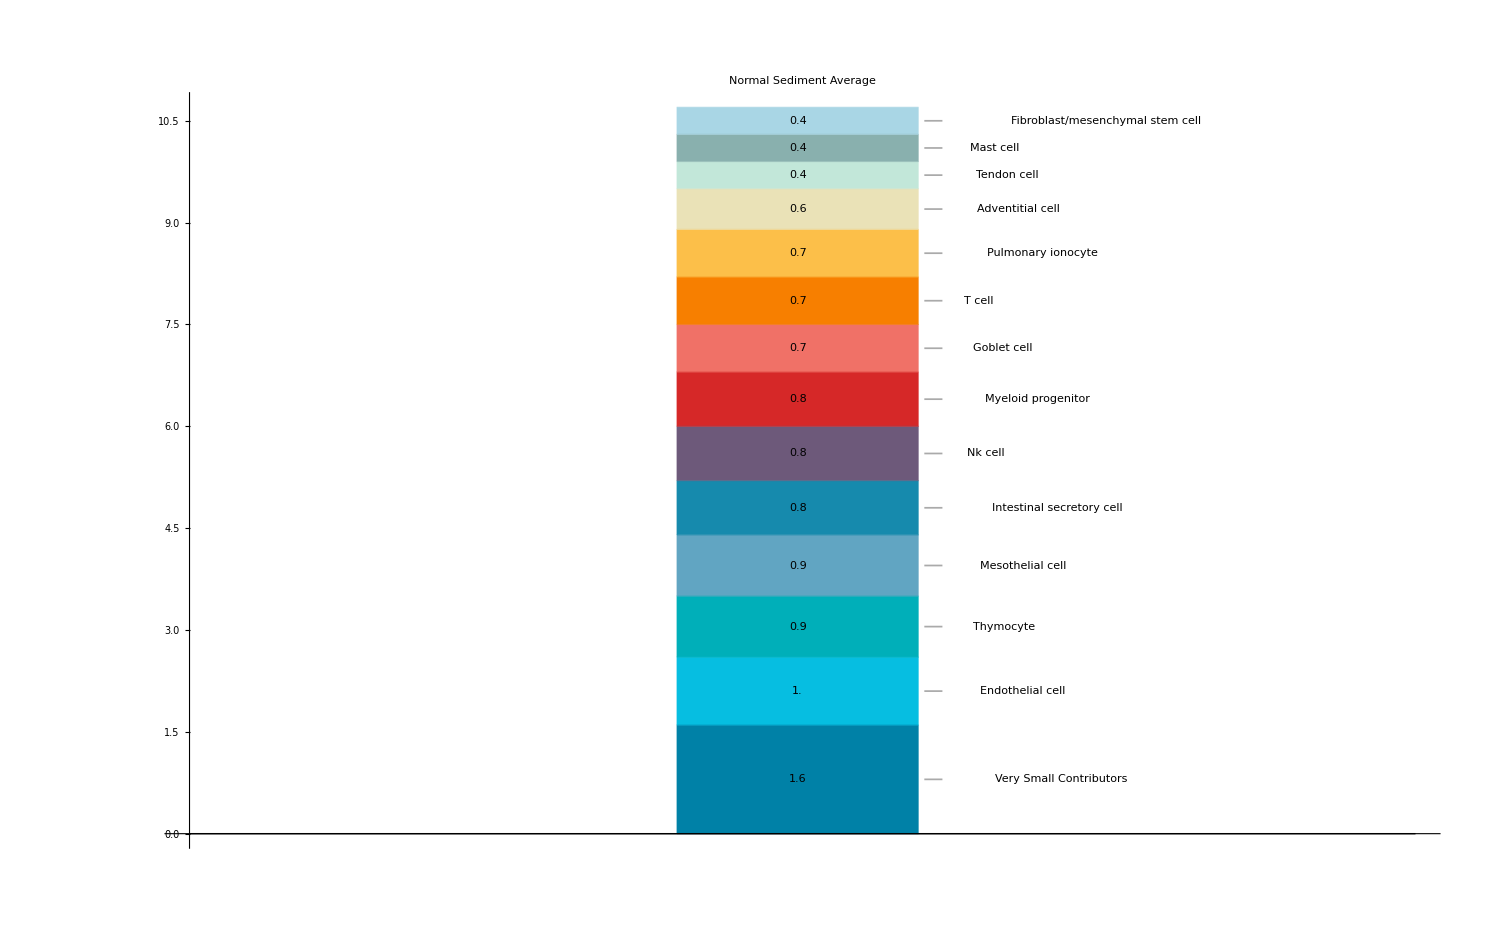

```mathematica
BarChart[shortlist,BarSpacing->2,ChartLayout->"Stacked",
ChartStyle-> barPal, ImageSize-> 1500, LabelingFunction ->( Placed[#1, Center]&), BaseStyle->{FontSize->20}, PlotLabel -> sampleCenter]
```

```mathematica
(* cool, now it's time to make the pie chart *)
```

```mathematica
gtPt1Percent = Position[Flatten[nonZeroVals], val_/;val  >=percentThresh ]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23}}

```mathematica
bigContribs = Part[nonZeroVals, #] &/@ gtPt1Percent
```

{{12.3},{9.8},{7.7},{6.8},{5.},{4.8},{4.6},{4.},{3.9},{3.7},{3.2},{3.1},{2.9},{2.7},{2.6},{2.2},{1.9},{1.7},{1.6},{1.5},{1.3},{1.1},{1.1}}

```mathematica
bigCells = Part[nonZeroCells, #] &/@ gtPt1Percent
```

{{Kidney epithelial cell},{Keratinocyte},{Prostate epithelia},{Salivary gland cell},{Intestinal enterocyte},{Mature conventional dendritic cell},{Ionocyte/luminal epithelial cell of mammary gland},{Luminal cell of prostate epithelium},{Intestinal tuft cell},{Neutrophil},{B cell},{Intrahepatic cholangiocyte},{Macrophage},{Bladder urothelial cell},{Monocyte},{Plasmablast},{Stromal cell},{Respiratory ciliated cell},{Schwann cell},{Basal cell},{Pericyte cell},{Salivary/bronchial secretory cell},{Hepatocyte}}

```mathematica
bigTot = Total[Flatten[bigContribs]] ;
smallContribTot = Total[Flatten[goodSmallVals]];
bigTot + smallContribTot (* cool, so we sum to 1 between small and big contributions *)
```

100.2

```mathematica
(* add the sum of the small contributions *)
```

```mathematica
bigContribs= AppendTo[bigContribs, {smallContribTot}];
bigCells = AppendTo[bigCells, {"Small"}]
```

{{Kidney epithelial cell},{Keratinocyte},{Prostate epithelia},{Salivary gland cell},{Intestinal enterocyte},{Mature conventional dendritic cell},{Ionocyte/luminal epithelial cell of mammary gland},{Luminal cell of prostate epithelium},{Intestinal tuft cell},{Neutrophil},{B cell},{Intrahepatic cholangiocyte},{Macrophage},{Bladder urothelial cell},{Monocyte},{Plasmablast},{Stromal cell},{Respiratory ciliated cell},{Schwann cell},{Basal cell},{Pericyte cell},{Salivary/bronchial secretory cell},{Hepatocyte},{Small}}

```mathematica
Total[Flatten[bigContribs]]
```

100.2

```mathematica
(* now it's time to sort it from big to small *)
```

```mathematica
finalOrderBig = Reverse[Ordering[bigContribs]];
bigContribs = Flatten[Part[bigContribs, #] &/@ finalOrderBig];
bigCells = Flatten[Part[bigCells, #] &/@ finalOrderBig];
```

```mathematica
(* make the labels for the pie chart *)
```

```mathematica
bigContribs
```

{12.3,10.7,9.8,7.7,6.8,5.,4.8,4.6,4.,3.9,3.7,3.2,3.1,2.9,2.7,2.6,2.2,1.9,1.7,1.6,1.5,1.3,1.1,1.1}

```mathematica
test = Callout[bigContribs[[#]], bigCells[[#]],  Appearance -> "Leader"]&/@ Range[Length[bigCells]]
```

{Callout[12.3,Kidney epithelial cell,Appearance→Leader],Callout[10.7,Small,Appearance→Leader],Callout[9.8,Keratinocyte,Appearance→Leader],Callout[7.7,Prostate epithelia,Appearance→Leader],Callout[6.8,Salivary gland cell,Appearance→Leader],Callout[5.,Intestinal enterocyte,Appearance→Leader],Callout[4.8,Mature conventional dendritic cell,Appearance→Leader],Callout[4.6,Ionocyte/luminal epithelial cell of mammary gland,Appearance→Leader],Callout[4.,Luminal cell of prostate epithelium,Appearance→Leader],Callout[3.9,Intestinal tuft cell,Appearance→Leader],Callout[3.7,Neutrophil,Appearance→Leader],Callout[3.2,B cell,Appearance→Leader],Callout[3.1,Intrahepatic cholangiocyte,Appearance→Leader],Callout[2.9,Macrophage,Appearance→Leader],Callout[2.7,Bladder urothelial cell,Appearance→Leader],Callout[2.6,Monocyte,Appearance→Leader],Callout[2.2,Plasmablast,Appearance→Leader],Callout[1.9,Stromal cell,Appearance→Leader],Callout[1.7,Respiratory ciliated cell,Appearance→Leader],Callout[1.6,Schwann cell,Appearance→Leader],Callout[1.5,Basal cell,Appearance→Leader],Callout[1.3,Pericyte cell,Appearance→Leader],Callout[1.1,Hepatocyte,Appearance→Leader],Callout[1.1,Salivary/bronchial secretory cell,Appearance→Leader]}

```mathematica
"#84a98c"
```

#84a98c

```mathematica
piePal = Map [RGBColor,{"#bee9e8" ,"#62b6cb","#1b4965","#cae9ff","#5fa8d3",  "#a4508b", "#BC412B","#f26419","#f8c7cc", "#f7567c","#7e1946", "#f6ae2d", "#68b0ab","#84a98c", "#5bba6f", "#9ece9a", "#c8d5b9", "#355070","#6d597a","#b56576","#e56b6f","#eaac8b","#89b0ae",  "#457b9d","#555b6e","#6096ba","#014f86"}]
```

{RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.10588235294117647, 0.28627450980392155, 0.396078431372549],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.6431372549019608, 0.3137254901960784, 0.5450980392156862],RGBColor[0.7372549019607844, 0.2549019607843137, 0.16862745098039217],RGBColor[0.9490196078431372, 0.39215686274509803, 0.09803921568627451],RGBColor[0.9725490196078431, 0.7803921568627451, 0.8],RGBColor[0.9686274509803922, 0.33725490196078434, 0.48627450980392156],RGBColor[0.49411764705882355, 0.09803921568627451, 0.27450980392156865],RGBColor[0.9647058823529412, 0.6823529411764706, 0.17647058823529413],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.5176470588235295, 0.6627450980392157, 0.5490196078431373],RGBColor[0.3568627450980392, 0.7294117647058823, 0.43529411764705883],RGBColor[0.6196078431372549, 0.807843137254902, 0.6039215686274509],RGBColor[0.7843137254901961, 0.8352941176470589, 0.7254901960784313],RGBColor[0.20784313725490197, 0.3137254901960784, 0.4392156862745098],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[0.8980392156862745, 0.4196078431372549, 0.43529411764705883],RGBColor[0.9176470588235294, 0.6745098039215687, 0.5450980392156862],RGBColor[0.5372549019607843, 0.6901960784313725, 0.6823529411764706],RGBColor[0.27058823529411763, 0.4823529411764706, 0.615686274509804],RGBColor[0.3333333333333333, 0.3568627450980392, 0.43137254901960786],RGBColor[0.3764705882352941, 0.5882352941176471, 0.7294117647058823],RGBColor[0.00392156862745098, 0.30980392156862746, 0.5254901960784314]}

```mathematica
piePal =Map[RGBColor, {
(* "#ffc857",*)

 (* added today *)

"#ffd000",

"#ffaa00",
(* "#ff7b00",
"#ff7f51",*)
"#f25c54",

"#d90368",
(* "#ff637d",
"#f88dad",*)


"#D81E5B",
"#a53860",

(*"#d90429", "#ff5a5f",*)

"#6d597a",


"#0c6291",
"#247BA0",



"#90e0ef",
"#5fa8d3",

"#62b6cb",
"#A0CED9",
"#bee9e8" ,
"#0075a2","#cae9ff","#3e92cc",






"#83C5BE",
"#028090",
"#68B0AB",
"#8FC0A9",
"#218380",
"#489fb5",
"#0C7B9E",
"#489fb5"
}]
```

{RGBColor[1., 0.8156862745098039, 0.],RGBColor[1., 0.6666666666666666, 0.],RGBColor[0.9490196078431372, 0.3607843137254902, 0.32941176470588235],RGBColor[0.8509803921568627, 0.011764705882352941, 0.40784313725490196],RGBColor[0.8470588235294118, 0.11764705882352941, 0.3568627450980392],RGBColor[0.6470588235294118, 0.2196078431372549, 0.3764705882352941],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.047058823529411764, 0.3843137254901961, 0.5686274509803921],RGBColor[0.1411764705882353, 0.4823529411764706, 0.6274509803921569],RGBColor[0.5647058823529412, 0.8784313725490196, 0.9372549019607843],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.6274509803921569, 0.807843137254902, 0.8509803921568627],RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0., 0.4588235294117647, 0.6352941176470588],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.24313725490196078, 0.5725490196078431, 0.8],RGBColor[0.5137254901960784, 0.7725490196078432, 0.7450980392156863],RGBColor[0.00784313725490196, 0.5019607843137255, 0.5647058823529412],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.5607843137254902, 0.7529411764705882, 0.6627450980392157],RGBColor[0.12941176470588237, 0.5137254901960784, 0.5019607843137255],RGBColor[0.2823529411764706, 0.6235294117647059, 0.7098039215686275],RGBColor[0.047058823529411764, 0.4823529411764706, 0.6196078431372549],RGBColor[0.2823529411764706, 0.6235294117647059, 0.7098039215686275]}

```mathematica
PieChart[test, ChartStyle->piePal, SectorOrigin->{ -1.05Pi / 3,1},BaseStyle->{FontSize->20},  ImageSize-> 1500,ImagePadding->{{240,60},{0,0}},LabelingFunction ->"RadialCenter", PlotLabel->sampleCenter]
```

-Graphics-

```mathematica
(* Good stuff, back out the corresponding dictionaries based on normal sediment and feed to the other 3 scripts*)
```

```mathematica
cellDict = Association[];
cellDict= Append[cellDict, bigCells[[#]] -> piePal[[#]]&/@Range[Length[bigCells]]] ;
```

```mathematica
cellDict = Append[cellDict, goodSmallCells[[#]] -> barPal[[#]] &/@ Range[Length[goodSmallCells]]]
```

<|Kidney epithelial cell→RGBColor[1., 0.8156862745098039, 0.],Small→RGBColor[1., 0.6666666666666666, 0.],Keratinocyte→RGBColor[0.9490196078431372, 0.3607843137254902, 0.32941176470588235],Prostate epithelia→RGBColor[0.8509803921568627, 0.011764705882352941, 0.40784313725490196],Salivary gland cell→RGBColor[0.8470588235294118, 0.11764705882352941, 0.3568627450980392],Intestinal enterocyte→RGBColor[0.6470588235294118, 0.2196078431372549, 0.3764705882352941],Mature conventional dendritic cell→RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],Ionocyte/luminal epithelial cell of mammary gland→RGBColor[0.047058823529411764, 0.3843137254901961, 0.5686274509803921],Luminal cell of prostate epithelium→RGBColor[0.1411764705882353, 0.4823529411764706, 0.6274509803921569],Intestinal tuft cell→RGBColor[0.5647058823529412, 0.8784313725490196, 0.9372549019607843],Neutrophil→RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],B cell→RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],Intrahepatic cholangiocyte→RGBColor[0.6274509803921569, 0.807843137254902, 0.8509803921568627],Macrophage→RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],Bladder urothelial cell→RGBColor[0., 0.4588235294117647, 0.6352941176470588],Monocyte→RGBColor[0.792156862745098, 0.9137254901960784, 1.],Plasmablast→RGBColor[0.24313725490196078, 0.5725490196078431, 0.8],Stromal cell→RGBColor[0.5137254901960784, 0.7725490196078432, 0.7450980392156863],Respiratory ciliated cell→RGBColor[0.00784313725490196, 0.5019607843137255, 0.5647058823529412],Schwann cell→RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],Basal cell→RGBColor[0.5607843137254902, 0.7529411764705882, 0.6627450980392157],Pericyte cell→RGBColor[0.12941176470588237, 0.5137254901960784, 0.5019607843137255],Hepatocyte→RGBColor[0.2823529411764706, 0.6235294117647059, 0.7098039215686275],Salivary/bronchial secretory cell→RGBColor[0.047058823529411764, 0.4823529411764706, 0.6196078431372549],Very Small Contributors→RGBColor[0., 0.5058823529411764, 0.6549019607843137],Endothelial cell→RGBColor[0.023529411764705882, 0.7450980392156863, 0.8823529411764706],Thymocyte→RGBColor[0., 0.6862745098039216, 0.7254901960784313],Mesothelial cell→RGBColor[0.3803921568627451, 0.6470588235294118, 0.7607843137254902],Intestinal secretory cell→RGBColor[0.08627450980392157, 0.5411764705882353, 0.6784313725490196],Nk cell→RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],Myeloid progenitor→RGBColor[0.8392156862745098, 0.1568627450980392, 0.1568627450980392],Goblet cell→RGBColor[0.9411764705882353, 0.44313725490196076, 0.403921568627451],T cell→RGBColor[0.9686274509803922, 0.4980392156862745, 0.],Pulmonary ionocyte→RGBColor[0.9882352941176471, 0.7490196078431373, 0.28627450980392155],Adventitial cell→RGBColor[0.9176470588235294, 0.8862745098039215, 0.7176470588235294],Tendon cell→RGBColor[0.7607843137254902, 0.9058823529411765, 0.8509803921568627],Mast cell→RGBColor[0.5372549019607843, 0.6901960784313725, 0.6823529411764706],Fibroblast/mesenchymal stem cell→RGBColor[0.6627450980392157, 0.8392156862745098, 0.8980392156862745]|>

```mathematica
otherCells = {"Basal cell of prostate epithelium", "Mast cell","Erythrocyte/erythroid progenitor","Pancreatic ductal cell"};
```

```mathematica
Append[cellDict, otherCells[[#]] -> barPal[[# + Length[goodSmallCells]]] &/@ Range[Length[otherCells]]]
```

<|Kidney epithelial cell→RGBColor[1., 0.8156862745098039, 0.],Small→RGBColor[1., 0.6666666666666666, 0.],Keratinocyte→RGBColor[0.9490196078431372, 0.3607843137254902, 0.32941176470588235],Prostate epithelia→RGBColor[0.8509803921568627, 0.011764705882352941, 0.40784313725490196],Salivary gland cell→RGBColor[0.8470588235294118, 0.11764705882352941, 0.3568627450980392],Intestinal enterocyte→RGBColor[0.6470588235294118, 0.2196078431372549, 0.3764705882352941],Mature conventional dendritic cell→RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],Ionocyte/luminal epithelial cell of mammary gland→RGBColor[0.047058823529411764, 0.3843137254901961, 0.5686274509803921],Luminal cell of prostate epithelium→RGBColor[0.1411764705882353, 0.4823529411764706, 0.6274509803921569],Intestinal tuft cell→RGBColor[0.5647058823529412, 0.8784313725490196, 0.9372549019607843],Neutrophil→RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],B cell→RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],Intrahepatic cholangiocyte→RGBColor[0.6274509803921569, 0.807843137254902, 0.8509803921568627],Macrophage→RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],Bladder urothelial cell→RGBColor[0., 0.4588235294117647, 0.6352941176470588],Monocyte→RGBColor[0.792156862745098, 0.9137254901960784, 1.],Plasmablast→RGBColor[0.24313725490196078, 0.5725490196078431, 0.8],Stromal cell→RGBColor[0.5137254901960784, 0.7725490196078432, 0.7450980392156863],Respiratory ciliated cell→RGBColor[0.00784313725490196, 0.5019607843137255, 0.5647058823529412],Schwann cell→RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],Basal cell→RGBColor[0.5607843137254902, 0.7529411764705882, 0.6627450980392157],Pericyte cell→RGBColor[0.12941176470588237, 0.5137254901960784, 0.5019607843137255],Hepatocyte→RGBColor[0.2823529411764706, 0.6235294117647059, 0.7098039215686275],Salivary/bronchial secretory cell→RGBColor[0.047058823529411764, 0.4823529411764706, 0.6196078431372549],Very Small Contributors→RGBColor[0., 0.5058823529411764, 0.6549019607843137],Endothelial cell→RGBColor[0.023529411764705882, 0.7450980392156863, 0.8823529411764706],Thymocyte→RGBColor[0., 0.6862745098039216, 0.7254901960784313],Mesothelial cell→RGBColor[0.3803921568627451, 0.6470588235294118, 0.7607843137254902],Intestinal secretory cell→RGBColor[0.08627450980392157, 0.5411764705882353, 0.6784313725490196],Nk cell→RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],Myeloid progenitor→RGBColor[0.8392156862745098, 0.1568627450980392, 0.1568627450980392],Goblet cell→RGBColor[0.9411764705882353, 0.44313725490196076, 0.403921568627451],T cell→RGBColor[0.9686274509803922, 0.4980392156862745, 0.],Pulmonary ionocyte→RGBColor[0.9882352941176471, 0.7490196078431373, 0.28627450980392155],Adventitial cell→RGBColor[0.9176470588235294, 0.8862745098039215, 0.7176470588235294],Tendon cell→RGBColor[0.7607843137254902, 0.9058823529411765, 0.8509803921568627],Fibroblast/mesenchymal stem cell→RGBColor[0.6627450980392157, 0.8392156862745098, 0.8980392156862745],Basal cell of prostate epithelium→RGBColor[0.49411764705882355, 0.7411764705882353, 0.7607843137254902],Mast cell→RGBColor[0.27450980392156865, 0.5607843137254902, 0.6862745098039216],Erythrocyte/erythroid progenitor→RGBColor[0.16470588235294117, 0.43529411764705883, 0.592156862745098],Pancreatic ductal cell→RGBColor[0.3568627450980392, 0.5215686274509804, 0.6666666666666666]|>

```mathematica
(* these cells are missing too: *)
{"Respiratory secretory cell", "Type ii pneumocyte", "Pancreatic pp cell", "Pancreatic acinar cell", "Cell of skeletal muscle", "Medullary thymic epithelial cell"}
```

{Respiratory secretory cell,Type ii pneumocyte,Pancreatic pp cell,Pancreatic acinar cell,Cell of skeletal muscle,Medullary thymic epithelial cell}